```mathematica
kd=KroneckerDelta;
d=Derivative;
```

```mathematica
Clear[t,r,θ,ϕ]
c=1;
G=1;

M=.25;
J=.5*M^2;


rs=(2*G*M)/c^2;
a=J/(M*c);
Σ=r^2+a^2 Cos[θ]^2;
Δ=r^2-rs*r+a^2;
gdd[x0_,x1_,x2_,x3_]=({{-(1-(rs*r)/Σ), 0, 0, -c*(rs*r*a*Sin[θ]^2)/Σ}, {0, Σ/Δ, 0, 0}, {0, 0, Σ, 0}, {-c*(rs*r*a*Sin[θ]^2)/Σ, 0, 0, (r^2+a^2+(rs*r*a^2)/Σ Sin[θ]^2)*Sin[θ]^2}})/.{t->x0,r->x1,θ->x2,ϕ->x3};

guu[x0_,x1_,x2_,x3_]=Inverse[gdd[x0,x1,x2,x3]];
```

```mathematica
(*Compute Christoffel Symbols*)Do[Γ1[i,j,k]=1/2(d[kd[j,0],kd[j,1],kd[j,2],kd[j,3]][gdd][x[0],x[1],x[2],x[3]][[i+1,k+1]]+d[kd[i,0],kd[i,1],kd[i,2],kd[i,3]][gdd][x[0],x[1],x[2],x[3]][[j+1,k+1]]-d[kd[k,0],kd[k,1],kd[k,2],kd[k,3]][gdd][x[0],x[1],x[2],x[3]][[i+1,j+1]]),{i,0,3},{j,0,3},{k,0,3}]
Do[Γ2[m,i,j]=Sum[guu[x[0],x[1],x[2],x[3]][[k+1,m+1]]Γ1[i,j,k],{k,0,3}],{m,0,3},{i,0,3},{j,0,3}]
```

```mathematica
(*geodesic Equation*)geodesicEqustions=Table[d[2][x[i]][s]+Sum[(Γ2[i,j,k]/.Table[x[p]->x[p][s],{p,0,3}])d[1][x[j]][s]d[1][x[k]][s],{j,0,3},{k,0,3}]==0,{i,0,3}];


initalLoc={0,6,π/4,0};
initalVel={vt,-1,0,0};(*in cordinate basis*)
initalVel=(initalVel/.vt->Max[vt/.Solve[initalVel.gdd@@initalLoc.initalVel==0,vt]]);

(*initalVel=initalVel/√Abs[initalVel.gdd@@initalLoc.initalVel];*)

initalLoction=Table[x[i][0]==initalLoc[[i+1]],{i,0,3}];
initalVelocity=Table[x[i]'[0]==initalVel[[i+1]],{i,0,3}];
geodesicEqustions//TableForm
initalLoction//TableForm
initalVelocity//TableForm
```

0.+2 ((Sin[x[2][s]]^2 (-(1. (x[1][s])^2)/((0.015625 Cos[x[2][s]]^2+(x[1][s])^2)^2)+0.5/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)) (0.015625+(x[1][s])^2+(0.0078125 Sin[x[2][s]]^2 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)))/(2 (0.-0.015625 Sin[x[2][s]]^2-Sin[x[2][s]]^2 (x[1][s])^2+(0.0078125 Sin[x[2][s]]^2 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)-(0.0078125 Sin[x[2][s]]^4 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)+(0.5 Sin[x[2][s]]^2 (x[1][s])^3)/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)))+((0.015625-0.5 x[1][s]+(x[1][s])^2) ((0.125 Sin[x[2][s]]^2 (x[1][s])^2)/((0.015625 Cos[x[2][s]]^2+(x[1][s])^2)^2)-(0.0625 Sin[x[2][s]]^2)/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)) ((0.000976563 Cos[x[2][s]]^2 Sin[x[2][s]]^2 x[1][s])/(0.015625-0.5 x[1][s]+(x[1][s])^2)+(0.0625 Sin[x[2][s]]^2 (x[1][s])^3)/(0.015625-0.5 x[1][s]+(x[1][s])^2)))/(2 (0.015625 Cos[x[2][s]]^2+(x[1][s])^2)^2 (0.-0.015625 Sin[x[2][s]]^2-Sin[x[2][s]]^2 (x[1][s])^2+(0.0078125 Sin[x[2][s]]^2 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)-(0.0078125 Sin[x[2][s]]^4 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)+(0.5 Sin[x[2][s]]^2 (x[1][s])^3)/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)))) x[0]'[s] x[1]'[s]+2 ((0.0078125 Cos[x[2][s]] Sin[x[2][s]]^3 x[1][s] (0.015625+(x[1][s])^2+(0.0078125 Sin[x[2][s]]^2 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)))/((0.015625 Cos[x[2][s]]^2+(x[1][s])^2)^2 (0.-0.015625 Sin[x[2][s]]^2-Sin[x[2][s]]^2 (x[1][s])^2+(0.0078125 Sin[x[2][s]]^2 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)-(0.0078125 Sin[x[2][s]]^4 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)+(0.5 Sin[x[2][s]]^2 (x[1][s])^3)/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)))+((0.015625-0.5 x[1][s]+(x[1][s])^2) (-(0.00195313 Cos[x[2][s]] Sin[x[2][s]]^3 x[1][s])/((0.015625 Cos[x[2][s]]^2+(x[1][s])^2)^2)-(0.125 Cos[x[2][s]] Sin[x[2][s]] x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)) ((0.000976563 Cos[x[2][s]]^2 Sin[x[2][s]]^2 x[1][s])/(0.015625-0.5 x[1][s]+(x[1][s])^2)+(0.0625 Sin[x[2][s]]^2 (x[1][s])^3)/(0.015625-0.5 x[1][s]+(x[1][s])^2)))/(2 (0.015625 Cos[x[2][s]]^2+(x[1][s])^2)^2 (0.-0.015625 Sin[x[2][s]]^2-Sin[x[2][s]]^2 (x[1][s])^2+(0.0078125 Sin[x[2][s]]^2 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)-(0.0078125 Sin[x[2][s]]^4 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)+(0.5 Sin[x[2][s]]^2 (x[1][s])^3)/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)))) x[0]'[s] x[2]'[s]+2 ((Sin[x[2][s]]^2 ((0.125 Sin[x[2][s]]^2 (x[1][s])^2)/((0.015625 Cos[x[2][s]]^2+(x[1][s])^2)^2)-(0.0625 Sin[x[2][s]]^2)/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)) (0.015625+(x[1][s])^2+(0.0078125 Sin[x[2][s]]^2 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)))/(2 (0.-0.015625 Sin[x[2][s]]^2-Sin[x[2][s]]^2 (x[1][s])^2+(0.0078125 Sin[x[2][s]]^2 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)-(0.0078125 Sin[x[2][s]]^4 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)+(0.5 Sin[x[2][s]]^2 (x[1][s])^3)/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)))+(Sin[x[2][s]]^2 (0.015625-0.5 x[1][s]+(x[1][s])^2) (2 x[1][s]-(0.015625 Sin[x[2][s]]^2 (x[1][s])^2)/((0.015625 Cos[x[2][s]]^2+(x[1][s])^2)^2)+(0.0078125 Sin[x[2][s]]^2)/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)) ((0.000976563 Cos[x[2][s]]^2 Sin[x[2][s]]^2 x[1][s])/(0.015625-0.5 x[1][s]+(x[1][s])^2)+(0.0625 Sin[x[2][s]]^2 (x[1][s])^3)/(0.015625-0.5 x[1][s]+(x[1][s])^2)))/(2 (0.015625 Cos[x[2][s]]^2+(x[1][s])^2)^2 (0.-0.015625 Sin[x[2][s]]^2-Sin[x[2][s]]^2 (x[1][s])^2+(0.0078125 Sin[x[2][s]]^2 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)-(0.0078125 Sin[x[2][s]]^4 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)+(0.5 Sin[x[2][s]]^2 (x[1][s])^3)/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)))) x[1]'[s] x[3]'[s]+2 ((Sin[x[2][s]]^2 (-(0.00195313 Cos[x[2][s]] Sin[x[2][s]]^3 x[1][s])/((0.015625 Cos[x[2][s]]^2+(x[1][s])^2)^2)-(0.125 Cos[x[2][s]] Sin[x[2][s]] x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)) (0.015625+(x[1][s])^2+(0.0078125 Sin[x[2][s]]^2 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)))/(2 (0.-0.015625 Sin[x[2][s]]^2-Sin[x[2][s]]^2 (x[1][s])^2+(0.0078125 Sin[x[2][s]]^2 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)-(0.0078125 Sin[x[2][s]]^4 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)+(0.5 Sin[x[2][s]]^2 (x[1][s])^3)/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)))+((0.015625-0.5 x[1][s]+(x[1][s])^2) ((0.000976563 Cos[x[2][s]]^2 Sin[x[2][s]]^2 x[1][s])/(0.015625-0.5 x[1][s]+(x[1][s])^2)+(0.0625 Sin[x[2][s]]^2 (x[1][s])^3)/(0.015625-0.5 x[1][s]+(x[1][s])^2)) (Sin[x[2][s]]^2 ((0.000244141 Cos[x[2][s]] Sin[x[2][s]]^3 x[1][s])/((0.015625 Cos[x[2][s]]^2+(x[1][s])^2)^2)+(0.015625 Cos[x[2][s]] Sin[x[2][s]] x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2))+2 Cos[x[2][s]] Sin[x[2][s]] (0.015625+(x[1][s])^2+(0.0078125 Sin[x[2][s]]^2 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2))))/(2 (0.015625 Cos[x[2][s]]^2+(x[1][s])^2)^2 (0.-0.015625 Sin[x[2][s]]^2-Sin[x[2][s]]^2 (x[1][s])^2+(0.0078125 Sin[x[2][s]]^2 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)-(0.0078125 Sin[x[2][s]]^4 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)+(0.5 Sin[x[2][s]]^2 (x[1][s])^3)/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)))) x[2]'[s] x[3]'[s]+x[0]''[s]==0
0.+(0.+((0.015625-0.5 x[1][s]+(x[1][s])^2) ((1. (x[1][s])^2)/((0.015625 Cos[x[2][s]]^2+(x[1][s])^2)^2)-0.5/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)))/(2 (0.015625 Cos[x[2][s]]^2+(x[1][s])^2))) (x[0]'[s])^2+(0.+((0.015625-0.5 x[1][s]+(x[1][s])^2) (-((-0.5+2 x[1][s]) (0.015625 Cos[x[2][s]]^2+(x[1][s])^2))/((0.015625-0.5 x[1][s]+(x[1][s])^2)^2)+(2 x[1][s])/(0.015625-0.5 x[1][s]+(x[1][s])^2)))/(2 (0.015625 Cos[x[2][s]]^2+(x[1][s])^2))) (x[1]'[s])^2-(0.03125 Cos[x[2][s]] Sin[x[2][s]] x[1]'[s] x[2]'[s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)+(0.-(x[1][s] (0.015625-0.5 x[1][s]+(x[1][s])^2))/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)) (x[2]'[s])^2+((0.015625-0.5 x[1][s]+(x[1][s])^2) (-(0.125 Sin[x[2][s]]^2 (x[1][s])^2)/((0.015625 Cos[x[2][s]]^2+(x[1][s])^2)^2)+(0.0625 Sin[x[2][s]]^2)/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)) x[0]'[s] x[3]'[s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)-(Sin[x[2][s]]^2 (0.015625-0.5 x[1][s]+(x[1][s])^2) (2 x[1][s]-(0.015625 Sin[x[2][s]]^2 (x[1][s])^2)/((0.015625 Cos[x[2][s]]^2+(x[1][s])^2)^2)+(0.0078125 Sin[x[2][s]]^2)/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)) (x[3]'[s])^2)/(2 (0.015625 Cos[x[2][s]]^2+(x[1][s])^2))+x[1]''[s]==0
0.-(0.0078125 Cos[x[2][s]] Sin[x[2][s]] x[1][s] (x[0]'[s])^2)/((0.015625 Cos[x[2][s]]^2+(x[1][s])^2)^3)+(0.015625 Cos[x[2][s]] Sin[x[2][s]] (x[1]'[s])^2)/((0.015625 Cos[x[2][s]]^2+(x[1][s])^2) (0.015625-0.5 x[1][s]+(x[1][s])^2))+2 (0.+(x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)) x[1]'[s] x[2]'[s]-(0.015625 Cos[x[2][s]] Sin[x[2][s]] (x[2]'[s])^2)/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)+(((0.00195313 Cos[x[2][s]] Sin[x[2][s]]^3 x[1][s])/((0.015625 Cos[x[2][s]]^2+(x[1][s])^2)^2)+(0.125 Cos[x[2][s]] Sin[x[2][s]] x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)) x[0]'[s] x[3]'[s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)+((-Sin[x[2][s]]^2 ((0.000244141 Cos[x[2][s]] Sin[x[2][s]]^3 x[1][s])/((0.015625 Cos[x[2][s]]^2+(x[1][s])^2)^2)+(0.015625 Cos[x[2][s]] Sin[x[2][s]] x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2))-2 Cos[x[2][s]] Sin[x[2][s]] (0.015625+(x[1][s])^2+(0.0078125 Sin[x[2][s]]^2 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2))) (x[3]'[s])^2)/(2 (0.015625 Cos[x[2][s]]^2+(x[1][s])^2))+x[2]''[s]==0
0.+2 ((((0.125 Sin[x[2][s]]^2 (x[1][s])^2)/((0.015625 Cos[x[2][s]]^2+(x[1][s])^2)^2)-(0.0625 Sin[x[2][s]]^2)/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)) (-1+(0.5 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)))/(2 (0.-0.015625 Sin[x[2][s]]^2-Sin[x[2][s]]^2 (x[1][s])^2+(0.0078125 Sin[x[2][s]]^2 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)-(0.0078125 Sin[x[2][s]]^4 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)+(0.5 Sin[x[2][s]]^2 (x[1][s])^3)/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)))+((0.015625-0.5 x[1][s]+(x[1][s])^2) (-(1. (x[1][s])^2)/((0.015625 Cos[x[2][s]]^2+(x[1][s])^2)^2)+0.5/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)) ((0.000976563 Cos[x[2][s]]^2 Sin[x[2][s]]^2 x[1][s])/(0.015625-0.5 x[1][s]+(x[1][s])^2)+(0.0625 Sin[x[2][s]]^2 (x[1][s])^3)/(0.015625-0.5 x[1][s]+(x[1][s])^2)))/(2 (0.015625 Cos[x[2][s]]^2+(x[1][s])^2)^2 (0.-0.015625 Sin[x[2][s]]^2-Sin[x[2][s]]^2 (x[1][s])^2+(0.0078125 Sin[x[2][s]]^2 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)-(0.0078125 Sin[x[2][s]]^4 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)+(0.5 Sin[x[2][s]]^2 (x[1][s])^3)/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)))) x[0]'[s] x[1]'[s]+2 (((-1+(0.5 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)) (-(0.00195313 Cos[x[2][s]] Sin[x[2][s]]^3 x[1][s])/((0.015625 Cos[x[2][s]]^2+(x[1][s])^2)^2)-(0.125 Cos[x[2][s]] Sin[x[2][s]] x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)))/(2 (0.-0.015625 Sin[x[2][s]]^2-Sin[x[2][s]]^2 (x[1][s])^2+(0.0078125 Sin[x[2][s]]^2 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)-(0.0078125 Sin[x[2][s]]^4 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)+(0.5 Sin[x[2][s]]^2 (x[1][s])^3)/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)))+(0.0078125 Cos[x[2][s]] Sin[x[2][s]] x[1][s] (0.015625-0.5 x[1][s]+(x[1][s])^2) ((0.000976563 Cos[x[2][s]]^2 Sin[x[2][s]]^2 x[1][s])/(0.015625-0.5 x[1][s]+(x[1][s])^2)+(0.0625 Sin[x[2][s]]^2 (x[1][s])^3)/(0.015625-0.5 x[1][s]+(x[1][s])^2)))/((0.015625 Cos[x[2][s]]^2+(x[1][s])^2)^4 (0.-0.015625 Sin[x[2][s]]^2-Sin[x[2][s]]^2 (x[1][s])^2+(0.0078125 Sin[x[2][s]]^2 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)-(0.0078125 Sin[x[2][s]]^4 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)+(0.5 Sin[x[2][s]]^2 (x[1][s])^3)/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)))) x[0]'[s] x[2]'[s]+2 ((Sin[x[2][s]]^2 (2 x[1][s]-(0.015625 Sin[x[2][s]]^2 (x[1][s])^2)/((0.015625 Cos[x[2][s]]^2+(x[1][s])^2)^2)+(0.0078125 Sin[x[2][s]]^2)/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)) (-1+(0.5 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)))/(2 (0.-0.015625 Sin[x[2][s]]^2-Sin[x[2][s]]^2 (x[1][s])^2+(0.0078125 Sin[x[2][s]]^2 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)-(0.0078125 Sin[x[2][s]]^4 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)+(0.5 Sin[x[2][s]]^2 (x[1][s])^3)/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)))+((0.015625-0.5 x[1][s]+(x[1][s])^2) ((0.125 Sin[x[2][s]]^2 (x[1][s])^2)/((0.015625 Cos[x[2][s]]^2+(x[1][s])^2)^2)-(0.0625 Sin[x[2][s]]^2)/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)) ((0.000976563 Cos[x[2][s]]^2 Sin[x[2][s]]^2 x[1][s])/(0.015625-0.5 x[1][s]+(x[1][s])^2)+(0.0625 Sin[x[2][s]]^2 (x[1][s])^3)/(0.015625-0.5 x[1][s]+(x[1][s])^2)))/(2 (0.015625 Cos[x[2][s]]^2+(x[1][s])^2)^2 (0.-0.015625 Sin[x[2][s]]^2-Sin[x[2][s]]^2 (x[1][s])^2+(0.0078125 Sin[x[2][s]]^2 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)-(0.0078125 Sin[x[2][s]]^4 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)+(0.5 Sin[x[2][s]]^2 (x[1][s])^3)/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)))) x[1]'[s] x[3]'[s]+2 (((0.015625-0.5 x[1][s]+(x[1][s])^2) (-(0.00195313 Cos[x[2][s]] Sin[x[2][s]]^3 x[1][s])/((0.015625 Cos[x[2][s]]^2+(x[1][s])^2)^2)-(0.125 Cos[x[2][s]] Sin[x[2][s]] x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)) ((0.000976563 Cos[x[2][s]]^2 Sin[x[2][s]]^2 x[1][s])/(0.015625-0.5 x[1][s]+(x[1][s])^2)+(0.0625 Sin[x[2][s]]^2 (x[1][s])^3)/(0.015625-0.5 x[1][s]+(x[1][s])^2)))/(2 (0.015625 Cos[x[2][s]]^2+(x[1][s])^2)^2 (0.-0.015625 Sin[x[2][s]]^2-Sin[x[2][s]]^2 (x[1][s])^2+(0.0078125 Sin[x[2][s]]^2 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)-(0.0078125 Sin[x[2][s]]^4 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)+(0.5 Sin[x[2][s]]^2 (x[1][s])^3)/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)))+((-1+(0.5 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)) (Sin[x[2][s]]^2 ((0.000244141 Cos[x[2][s]] Sin[x[2][s]]^3 x[1][s])/((0.015625 Cos[x[2][s]]^2+(x[1][s])^2)^2)+(0.015625 Cos[x[2][s]] Sin[x[2][s]] x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2))+2 Cos[x[2][s]] Sin[x[2][s]] (0.015625+(x[1][s])^2+(0.0078125 Sin[x[2][s]]^2 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2))))/(2 (0.-0.015625 Sin[x[2][s]]^2-Sin[x[2][s]]^2 (x[1][s])^2+(0.0078125 Sin[x[2][s]]^2 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)-(0.0078125 Sin[x[2][s]]^4 x[1][s])/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)+(0.5 Sin[x[2][s]]^2 (x[1][s])^3)/(0.015625 Cos[x[2][s]]^2+(x[1][s])^2)))) x[2]'[s] x[3]'[s]+x[3]''[s]==0

x[0][0]==0
x[1][0]==6
x[2][0]==π/4
x[3][0]==0

x[0]'[0]==1.09076
x[1]'[0]==-1
x[2]'[0]==0
x[3]'[0]==0

```mathematica
smax=3;
integrationRules=NDSolve[Join[geodesicEqustions,initalLoction,initalVelocity],{x[0],x[1],x[2],x[3]},{s,0,smax}][[1]];

Show[ParametricPlot3D[{x[1][s]Sin[x[2][s]]Cos[x[3][s]],x[1][s]Sin[x[2][s]]Sin[x[3][s]],x[1][s]Cos[x[2][s]]}/.integrationRules,{s,0,smax},PlotRange->{{-1,1},{-1,1},{-1,1}}*10,AxesLabel->{"x1","x2","x3"}],
Graphics3D[{Gray,Arrow@Tube[{{-10,0,0},{10,0,0}}],Arrow@Tube[{{0,-10,0},{0,10,0}}],Arrow@Tube[{{0,0,-10},{0,0,10}}]},PlotRange->{{-1,1},{-1,1},{-1,1}}*10]]
```

-Graphics3D-

```mathematica
θ=7.5/8 π/2;
r=10;

obsO={0,r,θ,0};
obsT={1,0,0,0};
obsE={0,-1,0,0};
obsA={0,0,0,1/(r*Sin[θ])};
obsB={0,0,-1/r,0};

step=.0025;

ai=1.5;
ao=3;
dθ=.02*π;
```

```mathematica
dat=Timing@Table[

initalLoc=obsO;
initalVel={vt,0,0,0}+obsE+α*obsA+β*obsB;
initalVel=(initalVel/.vt->Min[vt/.Solve[initalVel.gdd@@initalLoc.initalVel==0,vt]]);

smax=30;
initalLoction=Table[x[i][0]==initalLoc[[i+1]],{i,0,3}];
initalVelocity=Table[x[i]'[0]==initalVel[[i+1]],{i,0,3}];
Reap[NDSolve[Join[geodesicEqustions,initalLoction,initalVelocity,{WhenEvent[ai<x[1][s]<ao&&(π-dθ)/2<x[2][s]<(π+dθ)/2||x[1][s]<1.1*1/2 (rs+√(-4 a^2+rs^2))||x[1][s]*Sin[x[2][s]]*Cos[x[3][s]]<-5||s>smax,{Sow[{s,x[0][s],x[1][s],x[2][s],x[3][s]}],"StopIntegration"}]}],{x[0],x[1],x[2],x[3]},{s,0,2smax}]][[2,1,1]],{α,-.4,.4,step},{β,-.4,.4,step}];
dat[[1]]
(*ArrayPlot@dat[[2]]
Which[#1>smax,Purple,#3<1.11rs,Red,True,If[Sign@Sin[2π*#3*Sin[#5]Sin[#4]]*Sign@Sin[2π*#3*Cos[#4]]==1,Green,Black]]&@@*)
Beep[]
```

1673.14

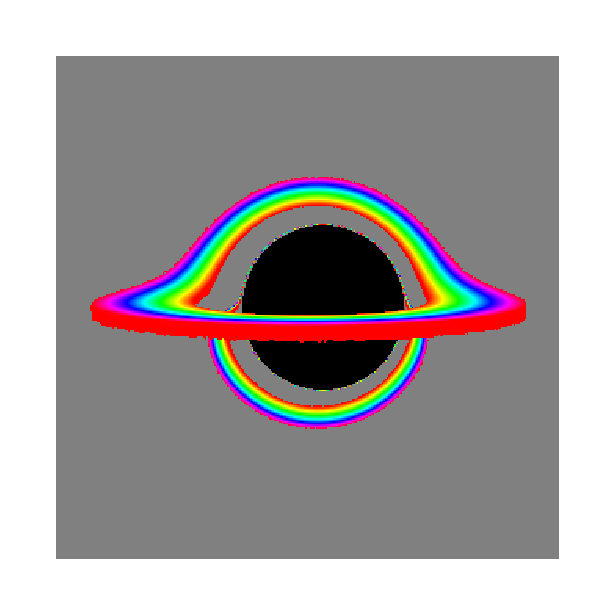

```mathematica
(*Graphics3D[{Sphere[{#3*Cos[#5]Sin[#4],#3*Sin[#5]Sin[#4],#3*Cos[#4]},.25]&@@@Flatten[dat[[2]],1],{Gray,Arrow@Tube[{{-10,0,0},{10,0,0}}],Arrow@Tube[{{0,-10,0},{0,10,0}}],Arrow@Tube[{{0,0,-10},{0,0,10}}]}},PlotRange->{{-1,1},{-1,1},{-1,1}}*10,Axes->True,AxesLabel->{"x1","x2","x3"}]*)
ArrayPlot@Reverse@Transpose@Map[Which[ai<=#3<=ao&&(π-dθ)/2<=#4<=(π+dθ)/2,Hue[#3/(ao-ai)],#1>=smax,(*Purple*)Gray,#3<1.11 1/2 (rs+√(-4 a^2+rs^2)),If[Sin[2*#4]Sin[4*#5]>0,(*Gray*)Black,Black],True,If[Sign@Sin[2π*#3*Sin[#5]Sin[#4]]*Sign@Sin[2π*#3*Cos[#4]]==1,(*Green*)Gray,(*Black*)Gray]]&@@#&,dat[[2]],{2}]
```